# Lab 2 : 3D Graphing and Contour Plots

In this lab, we will deal with functions of two variables. We will plot the graphs of some functions of two variables along with their contour maps. We will match contour maps with graphs. We will plot some level surfaces. 
We will be using the commands Plot3D and ContourPlot to study functions of two variables.

## 1. The basic Mathematica command for plotting a function of two variables is Plot3D. For example, if we wanted to plot z=x y e^(1-x^2-y^2)with plotting domain -2≤x≤2 and -2≤y≤2, we would do

```mathematica
Plot3D[x y E^(1-x^2-y^2),{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

Note that the above default viewpoint is different than what we are used to.
If we want the more standard viewpoint from the first octant, we can give a ViewPoint vector. For example,

```mathematica
Plot3D[x y E^(1-x^2-y^2),{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"},ViewPoint->{1,1,1}]
```

Plot the surface given by  z = Cos x Cos y. Choose the plotting domain yourself, but choose it so that we get a good feel for the behavior of the function. (Fill in and execute.) (Experiment until you get a nice picture.)

```mathematica
Plot3D[Cos[x] Cos[y],{x,... , ...},{y,... ,...},AxesLabel->{"x","y","z"},ViewPoint->{1,1,1}]
```

## 2. We can plot a contour map of level curves by using ContourPlot.

```mathematica
ContourPlot[x y E^(1-x^2-y^2),{x,-2,2},{y,-2,2},ContourLabels->True,ContourShading->False]
```

We can also adjust the number of level curves that are drawn by using more options:

```mathematica
ContourPlot[x y E^(1-x^2-y^2),{x,-2,2},{y,-2,2},Contours->15,ContourLabels->True,ContourShading->False]
```

Plot a contour map of the function  f(x,y) = Cos x Cos y  used in #1 above. Adjust the number of contours to get a good feel for the function. (Fill in and execute.)

```mathematica
ContourPlot[Cos[x] Cos[y],{x, ...,... },{y,... ,... },Contours->   ...          ,ContourLabels->True,ContourShading->False]
```

## 3. In this problem, we will match contour maps to given graphs. Below are six choices of contour maps. They are in the standard orientation.

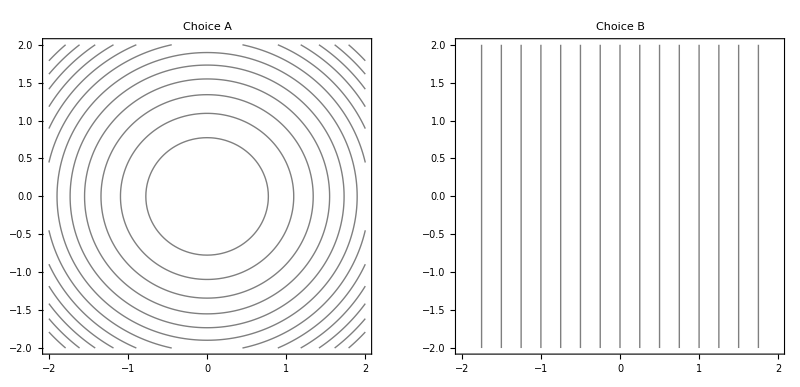

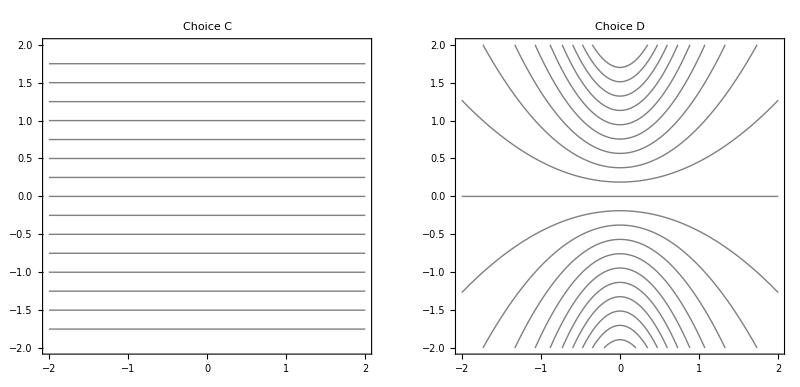

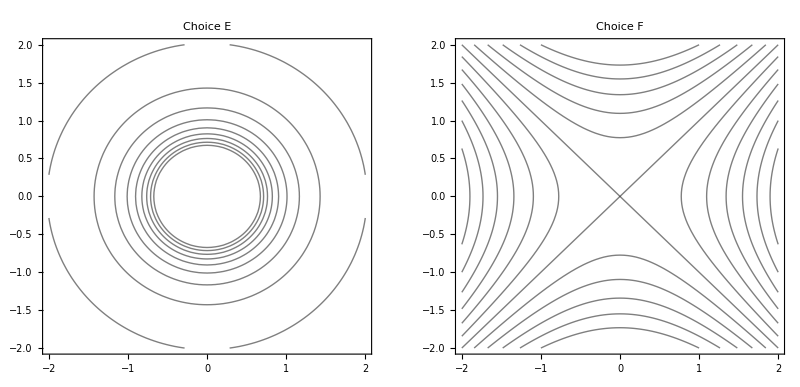

Next we have three graphs. These graphs are shown in standard viewpoint, feel free to rotate.

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Graph #1 corresponds to choice... because...

#### Graph #2 corresponds to choice... because...

#### Graph #3 corresponds to choice... because...

## 4. In this problem, we will match sets of level surfaces to given functions of three variables. Below are four choices of level surfaces and three functions.

Hint: pick a constant c and set f(x,y,z) equal to c to decide what kind of surface that would be.  You might need to do this for a few constants.

```mathematica
Choice 1
```

```mathematica
Choice 2
```

```mathematica
Choice 3
```

```mathematica
Choice 4
```

#### The function f(x,y,z)=y+z+1 matches choice... because...

#### The function f(x,y,z)=z-x2-y2 matches choice... because...

#### The function f(x,y,z)=y +√(x^2+z^2)matches choice... because...

## 5. In this problem, we’re looking at three level surfaces of the function g(x,y,z)=x^2-y^2-z^2 at the levels -1 , 0 , and +1. We’ve made the surfaces see-through (this is the opacity expression) so we can see all three surfaces.

```mathematica
ContourPlot3D[x^2-y^2-z^2,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,ContourStyle->Opacity[0.6],Contours->{-1,0,1}]
```

#### Identify which surface corresponds to which level. Response:

## 6. Consider the surface z=x^2-c y^2. Depending on the value of c, this surface will look like different quadric surfaces. Execute the command below and identify how the surface changes as c varies from -5 to 5.

```mathematica
Manipulate[Plot3D[x^2-c*y^2,{x,-2,2},{y,-2,2},Boxed->False,Axes->False],{c,-5,5,1}]
```

## 7. Exploratory Plotting

Use the graphing commands to plot some surfaces. For instance, try plotting

i. a plane which intersects x-axis at (3,0,0), y-axis at (0,4,0), and z-axis at (0,0,5).

```mathematica
Plot3D[...]
```

ii. a hemispherical dome above the XY -plane, that has radius 2 and center at (1, 1, 0).

```mathematica
Plot3D[...]
```

iii. a cone with vertex at the origin and the lateral surface making an angle of 45^◦ with the XY -plane.

```mathematica
Plot3D[...]
```